```mathematica
Clear["Global`*"]
```

```mathematica
scaling=1;
a=scaling N[14/10]; (* ==Carbon-Carbon Distance in A==*)
a0=√3 a;(* ==Lattice Constant Graphene in A==*) (*WARNING a0!=2.46,a0=2.42487*)
CouConst=8.987 10^9;
eCharge=1.602 10^-19;
ϵ=4.;
ω0=17.;
V=(eCharge^2 CouConst/(a0 10^-10 ϵ)) 6.241 10^18
V0=ω0/ϵ

(* == Direct Lattice == *)
a1=a0{1,0};  a2=a0{1/2,(√3)/2};                           (* == Direct Lattice Vectors == *)
kgr={0,0};  kpr=1/3*(2 a1-a2);                             (* == High symmetry points == *)
kmr=1/2(a1+a2);  kkr=1/3(a1-2 a2);

(* == Reciprocal Lattice == *)

{b1,b2}=2 π Inverse[Transpose[{a1,a2}]];  (* == Reciprocal Lattice Vectors == *)

b3=-( b1+b2);  
kg={0,0}; kp=1/3*(2 b1+b2);                             (* == High symmetry points == *)
km=1/2(b1+b2);  kk=1/3(b1+2 b2);

n=600;(*Nk=3 n^2*) (* n = number of points that the mesh of the full 1BZ (with same Δk distance) would have*)
δn=n; (* δn = parameter analogous to n, but for the mini-kmesh*)
λ=(n-δn); (* λ is used when generating the meshes*)
Nq=n; (*Nq = is the number of q points for which Π(q) will be calculated*)
{iqf,jqf}={0,Nq}; (*The indices of the vector pointing to the end of the q-path*)
(*In order to move in other direction, it might be convenient to project j along other kp vector*)
{i0,j0}={0,0}; (*Center of k mesh*)


(*This function transltes from indices i,j to vectors: *)
IndexToVector[kij_]:=Module[{sol},
sol=Table[kij[[i,j]].({a1,a2}/a0 ),{i,1,Length[kij]},{j,1,Length[kij[[i]]]}]
];

(*kij the indices of the vectors in the k-mesh: *)
R0ij=Module[{sol},
sol=Table[{N[i],N[j]},{i,-(n-λ),(n-λ)},{j,Max[-(n-λ),-(n-λ)-i],Min[(n-λ),(n-λ)-i]}]
];
R0ij= Delete[R0ij,Position[R0ij,{0.,0.}]];
R0ijmesh=IndexToVector[R0ij];
R0=Flatten[R0ij,1];
R0mesh=Flatten[R0ijmesh,1];
```

1.48404

4.25

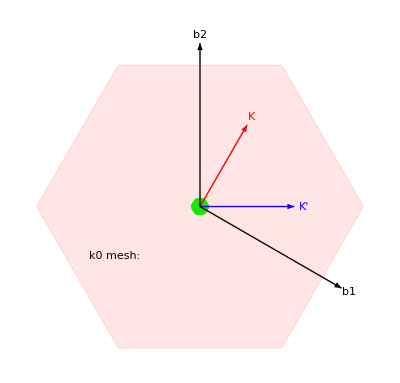

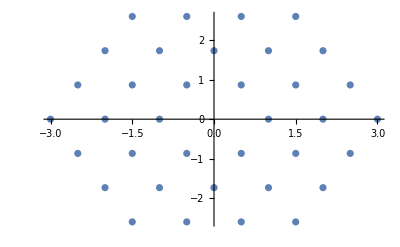

```mathematica
(*Drawing the contours and vectors of the 1BZ for the figures: *)
BZcontour = Polygon[{((4π)/(3a))*{-1,0},((4π)/(3a))*{(-1)/2,(√3)/2},((4π)/(3a))*{1/2,(√3)/2},((4π)/(3a))*{1,0},((4π)/(3a))*{1/2,(-√3)/2},((4π)/(3a))*{(-1)/2,(-√3)/2}}];
ps=0.015;
BZvectors =Graphics[{
Red,Arrow[{{0,0},kk}],
Blue,Arrow[{{0,0},kp}],
Black,Arrow[{{0,0},b1}],
Black,Arrow[{{0,0},b2}],
Black, Text["b1",b1*1.05],
Black, Text["b2",b2*1.05],
Red, Text["K",kk*1.1],
Blue, Text["K'",kp*1.1],
Red,Opacity[0.1],EdgeForm [Dashed],BZcontour
}];

(*Plotting the k mesh: *)

Show[
Graphics[{
Text["k0 mesh:",0.6b3],
PointSize[ps],
Green,
Point[R0mesh 0.03]
}],
BZvectors
]
ListPlot[R0mesh]
```

```mathematica
VC[qxa0_,qya0_]:=V0+V  Total[Exp[-ⅈ R0mesh.{qxa0,qya0}]/Map[Norm,R0mesh]];
```

{√(Abs[k1x]^2+Abs[k1y]^2),√(Abs[k2x]^2+Abs[k2y]^2),√(Abs[k3x]^2+Abs[k3y]^2)}

{ⅇ^(-ⅈ (k1x qxa0+k1y qya0)),ⅇ^(-ⅈ (k2x qxa0+k2y qya0)),ⅇ^(-ⅈ (k3x qxa0+k3y qya0))}

{ⅇ^(-ⅈ (k1x qxa0+k1y qya0))/(√(Abs[k1x]^2+Abs[k1y]^2)),ⅇ^(-ⅈ (k2x qxa0+k2y qya0))/(√(Abs[k2x]^2+Abs[k2y]^2)),ⅇ^(-ⅈ (k3x qxa0+k3y qya0))/(√(Abs[k3x]^2+Abs[k3y]^2))}

```mathematica
n=2600;
Nq=2n;
qstep=Nq/10;
Lq=2 Norm[kk];
Δq=Lq/Nq;
```

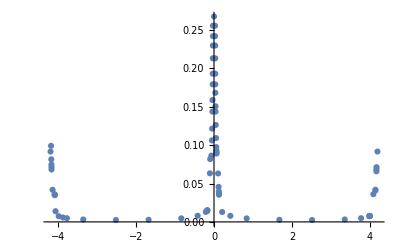

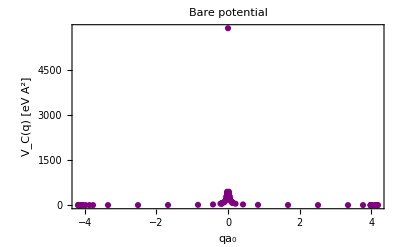

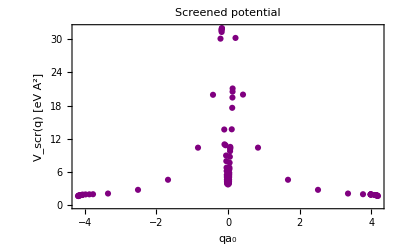

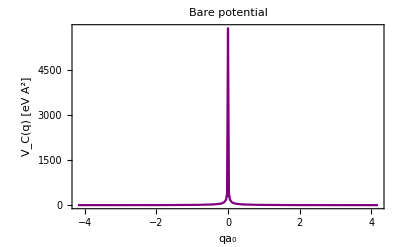

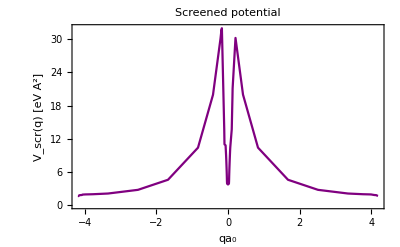

```mathematica
Πq0={{0,0.09164182381665663},{8,0.0990690176637428},{12,0.08148738683113614},{14,0.07464947215204142},{15,0.07122455515300888},{16,0.06826353589996159},{32,0.04180611679799731},{65,0.03601032767796678},{67,0.03493717635983178},{68,0.03490197045204574},{80,0.013906450763631355},{130,0.007418916359370244},{197,0.00575183576512536},{260,0.004797539475757213},{520,0.0031370862419986796},{1040,0.00244658740827661},{1560,0.0027714893609279375},{2080,0.004605257645724513},{2340,0.008000028938157053},{2470,0.013014223254407823},{2486,0.014205095225538011},{2490,0.014598522226497183},{2492,0.0148273898081107},{2493,0.01495244087342826},{2494,0.015085775705240782},{2535,0.06326248011417794},{2539,0.08182193211932352},{2558,0.08625736763708568},{2567,0.10616919889394977},{2571,0.12146547068091999},{2575,0.14367769584148443},{2577,0.1586383190097246},{2579,0.17913126895017004},{2580,0.1930169115717676},{2581,0.21301526083622502},{2582,0.2296596008933696},{2583,0.24187831775133628},{2584,0.25546187951332416},{2600,0.26752299394633466},{2616,0.25545385827231265},{2617,0.2418686838982373},{2618,0.22964815329214508},{2619,0.2130017884672088},{2620,0.19300119453995238},{2621,0.17911307972529109},{2622,0.16813134358924017},{2624,0.15058339568257442},{2625,0.14364724732410103},{2628,0.12623734340216808},{2632,0.10919327633533438},{2636,0.09735869464728979},{2638,0.09275661187811726},{2639,0.09076104615024665},{2640,0.08901545109721513},{2665,0.06307203872168776},{2673,0.04556438259085849},{2677,0.03970370685206649},{2679,0.036725452394995},{2680,0.0353505232860984},{2730,0.012870313437530135},{2860,0.007908122917349271},{3120,0.004560613684257954},{3640,0.002758212800321897},{4160,0.0024466658908028497},{4680,0.003146235995166162},{4940,0.004818467371490346},{5070,0.007458343743837404},{5074,0.007585705169654174},{5075,0.007618064789691721},{5076,0.007650648352151801},{5077,0.007683467687485855},{5078,0.007716537276082888},{5135,0.036069240034478346},{5167,0.04098899455829624},{5168,0.04185398639145778},{5183,0.06587348661257159},{5184,0.06828488286301805},{5185,0.07124496180904698},{5200,0.09164774586673703}};
qi= Table[{ Πq0[[i,1]]  Δq-Norm[kk],0.},{i,1,Length[Πq0]}];
Πq0q=Table[{qi[[i]],Πq0[[i,2]]},{i,1,Length[Πq0]}];
qia0= a0 Πq0q[[All,1]];
Π=Πq0[[All,2]];
ListPlot[Transpose[{qia0[[All,1]],Π}]]
Vcq=Apply[VC,qia0,{1}];
Vscr=Vcq/(1+Vcq Π);
Show[ListPlot[Transpose[{qia0[[All,1]],Vcq}], PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->False,Frame-> True,Axes->False, FrameLabel->{"qa_0","V_C(q) [eV A^2]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Bare potential"]]]
Show[ListPlot[Transpose[{qia0[[All,1]],Vscr}], PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->False,Frame-> True, Axes->False,FrameLabel->{"qa_0","V_scr(q) [eV A^2]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Screened potential"]]]
Show[ListPlot[Transpose[{qia0[[All,1]],Vcq}], PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->True,Frame-> True,Axes->False, FrameLabel->{"qa_0","V_C(q) [eV A^2]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Bare potential"]]]
Show[ListPlot[Transpose[{qia0[[All,1]],Vscr}], PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->True,Frame-> True, Axes->False,FrameLabel->{"qa_0","V_scr(q) [eV A^2]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Screened potential"]]]
(*
Vcq=Map[Vc,qia0,{1}];
Vscr=Vcq/(1+Vcq Π);*)
```

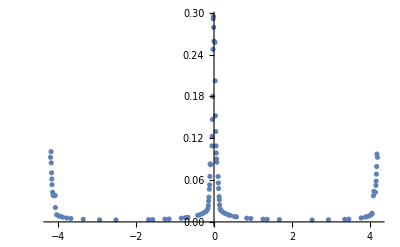

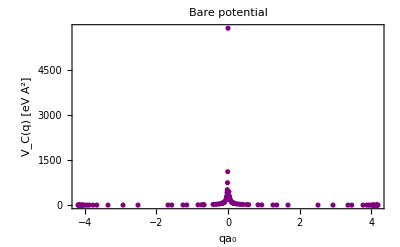

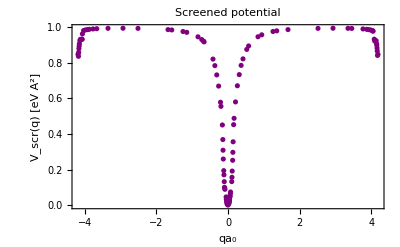

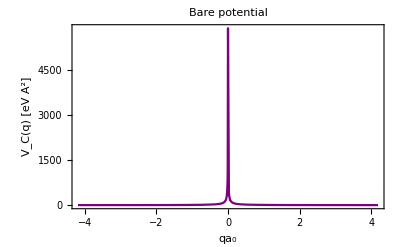

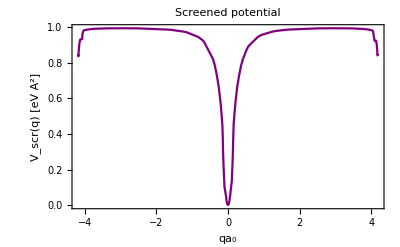

```mathematica
n=3600;
Nq=2n;
Lq=2 Norm[kk];
Δq=Lq/Nq;

Πq0={{0,0.09258129354506382},{11,0.10077135581840668},{16,0.08467606438054429},{22,0.0704328210954602},{27,0.061526473820630326},{33,0.053388942546999794},{45,0.042484518262381636},{56,0.0380392162852856},{90,0.037418095394847396},{101,0.037964866843389185},{106,0.020585245470504877},{135,0.010345538967768655},{180,0.008644932659639726},{225,0.007618522290172261},{270,0.006794018639714671},{360,0.005633100383867097},{450,0.004876084032677424},{720,0.0036810281002582685},{1080,0.0030575221880429354},{1440,0.002865496877943377},{2160,0.003239517285683206},{2250,0.003366236463376891},{2520,0.003917972104117998},{2610,0.004179895900929764},{2880,0.005366931488880142},{2970,0.005975507933654369},{3015,0.0063425368161054005},{3026,0.006439950391384242},{3240,0.009269681120191038},{3285,0.01022657165412057},{3330,0.011401889479373725},{3375,0.012878578786403083},{3420,0.014805517661478671},{3431,0.015382707395109944},{3465,0.018818445900670795},{3476,0.023450636356420848},{3481,0.02996730301535197},{3487,0.035460177653406505},{3498,0.04683521461734177},{3503,0.05306968574068068},{3510,0.06520159365178736},{3515,0.08286973732905133},{3521,0.08294064846720366},{3526,0.08207040444539047},{3555,0.10897145057327655},{3560,0.12268921744712195},{3566,0.14692316021915064},{3571,0.17988680572391363},{3577,0.24735389118379553},{3582,0.2913790382855974},{3588,0.29458277615451195},{3593,0.2788974995327081},{3600,0.2591124333314977},{3622,0.2574439584384983},{3627,0.20229622839562075},{3633,0.1521609330264021},{3638,0.12955922090709743},{3645,0.1089390397040794},{3650,0.09881440926355053},{3656,0.0902308728612677},{3661,0.08560808642170563},{3690,0.06506845505107971},{3695,0.05583018042875915},{3701,0.04782607144139546},{3712,0.036272617071586515},{3717,0.03163639171473139},{3723,0.024415268985977324},{3735,0.018684773484545017},{3746,0.017011472606801737},{3780,0.014693372278919578},{3825,0.012775162417930364},{3870,0.011309134336964972},{3915,0.010143643636315074},{3960,0.009195317818514898},{4050,0.0077519534143280135},{4095,0.007192513571367643},{4320,0.005330574634839204},{4410,0.004854032388163937},{4680,0.0038977564579997597},{4770,0.0036826904353452865},{5040,0.0032286558643963813},{5760,0.0028655248887661435},{6120,0.0030612008725332887},{6480,0.0036885366584052033},{6570,0.003976739937196425},{6840,0.005650405979640375},{6930,0.006818209722077145},{6975,0.007647226243714293},{7020,0.008676363978375928},{7065,0.010385465074429176},{7076,0.011480595923475877},{7081,0.012360211839464185},{7110,0.03746014397726189},{7121,0.043744956839424566},{7155,0.04250798554427697},{7166,0.05225689250570669},{7171,0.058465344327746596},{7177,0.06849141461846982},{7182,0.07939206719928482},{7188,0.09719855173681818},{7200,0.09258778911115795}};
qi= Table[{ Πq0[[i,1]]  Δq-Norm[kk],0.},{i,1,Length[Πq0]}];
Πq0q=Table[{qi[[i]],Πq0[[i,2]]},{i,1,Length[Πq0]}];
qia0= a0 Πq0q[[All,1]];
Π=Πq0[[All,2]];
ListPlot[Transpose[{qia0[[All,1]],Π}]]
Vcq=Apply[VC,qia0,{1}];
Vscr=1/(1+Vcq Π);
Show[ListPlot[Transpose[{qia0[[All,1]],Vcq}], PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->False,Frame-> True,Axes->False, FrameLabel->{"qa_0","V_C(q) [eV A^2]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Bare potential"]]]
Show[ListPlot[Transpose[{qia0[[All,1]],Vscr}], PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->False,Frame-> True, Axes->False,FrameLabel->{"qa_0","V_scr(q) [eV A^2]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Screened potential"]]]
Show[ListPlot[Transpose[{qia0[[All,1]],Vcq}], PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->True,Frame-> True,Axes->False, FrameLabel->{"qa_0","V_C(q) [eV A^2]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Bare potential"]]]
Show[ListPlot[Transpose[{qia0[[All,1]],Vscr}], PlotRange-> All(*{{0.,0.2},{0,200}}*),PlotStyle-> Purple,Joined->True,Frame-> True, Axes->False,FrameLabel->{"qa_0","V_scr(q) [eV A^2]"},LabelStyle->Directive[Black,15,FontFamily->"Times"],PlotLabel->Style["Screened potential"]]]
```

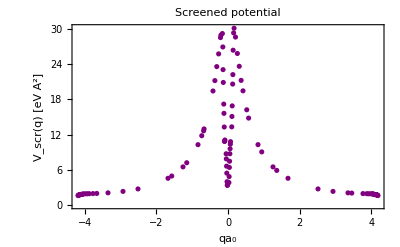

-Graphics-